```mathematica
init = {{1,1},{-1,1},{-1,-1},{1,-1},{1,1}}
(*まず、最初の4点の座標を定める*)
```

{{1,1},{-1,1},{-1,-1},{1,-1},{1,1}}

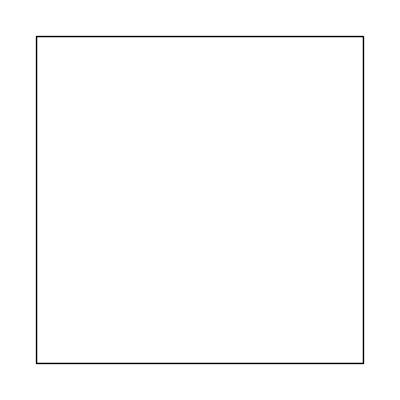

```mathematica
Show[Graphics[Line[init]]]
```

```mathematica
u = {{4/5,-1/5},{1/5,4/5}};
(*課題の結果をよく見ると、第６個の正方形は最初と同じ角度になると思って、
故に毎回五分の一を回転して縮小することであるかなと考えて、一度試してみると正しくなったかなと思っている。*)
```

```mathematica
{{4/5,-1/5},{1/5,4/5}}
```

```mathematica
rotate[p_]:=Map[u.#&,p];
(*ここでrotate関数を定義する、u.#&は純関数であり*)
```

```mathematica
p1=rotate[init];
```

```mathematica
p2=rotate[p1];
```

```mathematica
p3=rotate[p2];
```

```mathematica
p4=rotate[p3];
p5=rotate[p4];
```

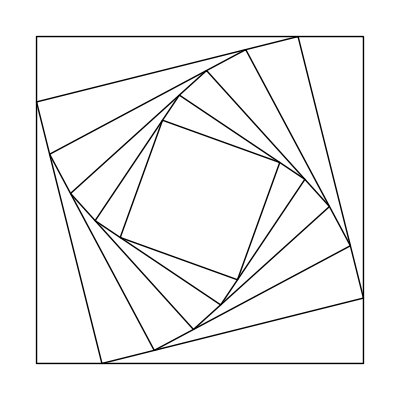

```mathematica
Show[Graphics[Line[{init,p1,p2,p3,p4,p5}]]]
(*ここで講義資料のように一回試してみた*)
```

```mathematica
Show[Graphics[Line[NestList[rotate,init,13]]]]
(*f を0から13回適用したNestList関数を使って、以下のような図を書けます*)
```

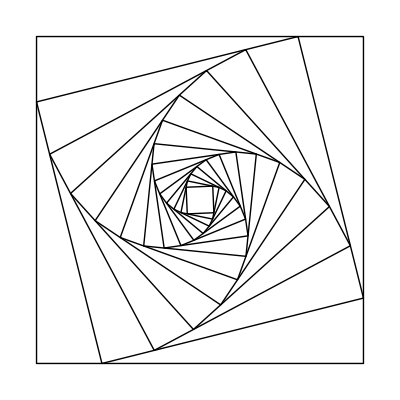

```mathematica
Clear["Global`*"]
```

```mathematica
Julia[c_]:=
Length[FixedPointList[#^2+0.3-0.01 I&,c,50,SameTest->(Abs[#2]≥100.&)]]-1
(*まず、FixedPointListを使って、ジュリア集合を定義する*)
```

```mathematica
DensityPlot[Julia[x+y I],{x,-1.2,1.2},
{y,-1.2,1.2},PlotPoints->100,
ColorFunction->"Monochrome",
PlotLegends->Automatic]
(*講義資料出た例と同じするようにgamma値を定義し、座標系のサイズと色の設定を確定して画像を生成する*)
```

DensityPlot::cfun: オプションColorFunction -> Monochromeの値が有効な色関数でも階調度のColorData実体でもありません．

-Graphics-

```mathematica
Clear["Global`*"]
```

```mathematica
(*自分興味あるジュリア集合を試してみよう*)
```

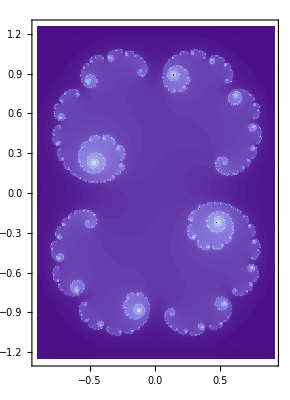

```mathematica
JuliaSetPlot[0.3-0.01 I,ColorFunction->"LakeColors"]
(*色のテストが、例と一番似ているのは"LakeColors"かなと考える*)
```

```mathematica
Clear["Global`*"]
```

```mathematica
(*色々試してみると、本当に面白いと思っている。*)
```

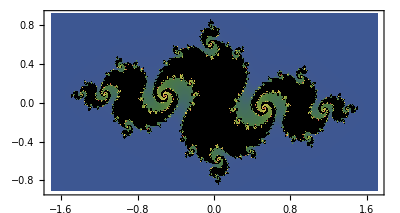

```mathematica
JuliaSetPlot[z^2-0.79+0.13I,z,ColorFunction->"DarkRainbow"]
```

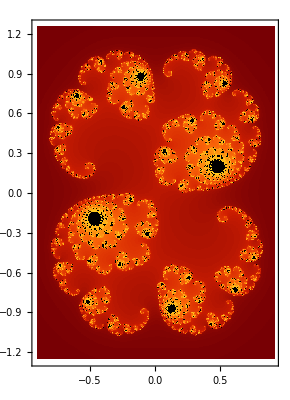

```mathematica
JuliaSetPlot[z^2+0.285+0.01 I,z,ColorFunction->"SolarColors"]
```

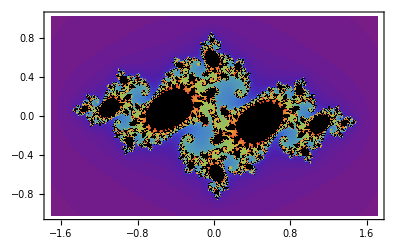

```mathematica
JuliaSetPlot[z^2-0.74543+0.11301 I,z,ColorFunction->"Rainbow"]
```